# Function Definitions

General Definitions
R[] means that this is the return type of a Function / Module

## BinPopGenerator

Generate a binary string population 

[numSamples_: number]	the number of samples
[strLength_: number]		the length of one sample

R[array<array<bit>>]		return the number of samples requested as binary arrays

```mathematica
ClearAll[BinPopGenerator];
```

```mathematica
BinPopGenerator[numSamples_, strlength_] :=Table[Random[Integer, {0,1}], {i,1,numSamples}, {j,1,strlength}];
```

```mathematica
BinPopGenerator[10, 5]
```

{{1,0,1,0,1},{0,1,1,0,0},{0,0,1,0,0},{1,1,0,0,0},{1,1,1,1,1},{1,1,1,0,1},{1,1,1,1,0},{0,0,1,1,1},{0,1,1,1,1},{1,0,0,1,0}}

## ffit

[x_: number]	the input value
R[number]	the result of the function

```mathematica
ClearAll[ffit];
```

```mathematica
ffit[x_] = 1+ Cos[x]/(1+0.01 x^2);
```

## Phenotype

```mathematica
ClearAll[Phenotype, PhenotypeBinToNum, PhenotypeFuncGen];
```

### PhenotypeBinToNum

```mathematica
PhenotypeBinToNum[bin_,space_]:= Module[
{erg = 0},
Do[erg += bin⟦i⟧*2^(i-1), {i,1,Length[bin]}];
Return[N[erg/(2^10)*space]]
]
```

### Phenotype

[x_: array<bit>]		the input value
OR [x_: array<array<bit>>]	array of input values
[space: number]		the space on which the phenotype is distributed onto

R[number]			matching of the input Phenotype(x) in the space
OR R[array<number>]

```mathematica
Phenotype[x_, space_] := Module[ {erg}, erg=0;
If[Length[Dimensions[x]] == 1, 
Return[PhenotypeBinToNum[x,space]]
,(*else*)
Return[Map[Function[{seq}, PhenotypeBinToNum[seq, space]], x]]
];
]
```

### PhenotypeFuncGen

[space: number]	the space on which the phenotype is distributed onto

R[function(x: array<bit>)] the function respecting the space

```mathematica
PhenotypeFuncGen[space_] := Function[{x},Phenotype[x,space] ]
```

### Tests

```mathematica
Phenotype[{1,1,1,1,1,1,1,1,1,1}, 2^3]
Phenotype[{0,0,0,0,0,0,0,0,0,0}, 2^3]
Phenotype[{{0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1}}, 2^3]
```

7.99219

0.

{0.,7.99219}

## SelectParent

[pop: Array<Array<bit>>]							the population
[fpheno_: function(pop: Array<Array<bit>>) -> Array<Array>>] : 		a function that maps to the phenotype

R[integer]									the array index of the parent

```mathematica
ClearAll[SelectParentByWheel];
```

```mathematica
SelectParentByWheel[pop_, fpheno_] := Module[{popFitness, totalFitness, wheel, elem, index},
popFitness = ffit[fpheno[pop]]; (*Calculates fitness(pheno(pop))*)
totalFitness = Fold[Plus,0,popFitness] ; (*Calculates sum(fitness(pheno(pop)))*)
wheel = FoldList[Plus, First[popFitness], Rest[popFitness]]; (*Array of summed up fitness scores [f1, f1+f2, f1+f2+f3]*)
(*WARNING: do not put this expression inside of the next statement, this results in an non-uniform distribution*)
number = RandomReal[{0,totalFitness}]; 
elem = First[Select[wheel, number<=#  &]];
index = Flatten[Position[wheel, elem]];
Return[First[index]]
]
```

### Tests

{{4,9864},{10,12918},{5,9792},{6,9999},{3,9823},{7,9782},{2,9964},{8,10037},{9,7900},{1,9921}}

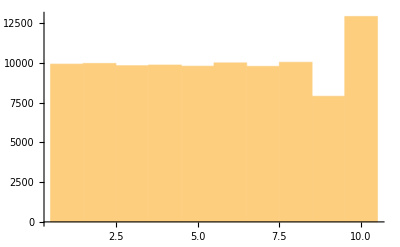

```mathematica
pop =BinPopGenerator[10,10];
fpheno :=Function[{x}, {1,1,1,1,1,1,1,1,5,0}];
t =Table[SelectParentByWheel[pop, fpheno], {i,1,100000}];
Tally[t]
Histogram[t, 10]
```

## InvertBit

[in_: bit]	the bit to be inverted

R[bit]		the inverted bit

```mathematica
ClearAll[InvertBit];
```

```mathematica
InvertBit[in_]  :=  Mod[2(in/2+0.5), 2]
```

## CrossOver

[p1_: array<bit>]	array of bits that describe the first parent chromosome
[p2_: array<bit>]	array of bits that describe the second parent chromosome
[pos_: integer]		the position where the crossover cut happens

R[array<bit>]		one child chromosome as array<bit>

```mathematica
ClearAll[CrossOver];
```

```mathematica
CrossOver[p1_, p2_, pos_] := Module[{child}, 
child = Join[Take[p1, pos], Drop[p2, pos]];
Return[child];
]
```

## Mutate

[chrom_: array<bit>] 		array of bits that describe the chromosome, 
[length_: integer] 		length of <chrom_>
[rate_: number] 		ratio of mutations added to the result

R[array<bit>]			Returns an array of bits representing the mutated chromosome

```mathematica
ClearAll[Mutate];
```

```mathematica
Mutate[chrom_,length_, rate_] := Module[{tmp}, 
tmp  = chrom;
Do[
If [Random []<rate, 
	(*Print["Mutated at pos: ",i];*)
	tmp⟦i⟧ = InvertBit[chrom⟦i⟧];
], {i,1,length}];
Return[tmp];
]
```

## EvolutionStep

[parent1_: array<bit>]								array of bits that describe the parent chromosome
[parent2_: array<bit>]								array of bits that describe the parent chromosome
[length_: integer] 								length of parent1 and parent2
[fpheno_: function(pop: Array<Array<bit>>) -> Array<Array>>] : 		a function that maps to the phenotype

R1[array<bit>]		child 1 from the parents 1 and 2
R2[array<bit>]		child 2 from the parents 1 and 2

```mathematica
ClearAll[EvolutionStep];
```

```mathematica
EvolutionStep[parent1_, parent2_, length_] := Module[
{pcross= 0.,pmut =  0.1,
crossat = 0,
child1, 
child2},
If[Random[]< pcross, crossat = Random[Integer, {1, length-1}]];
child1 =CrossOver[parent1, parent2, crossat];
child2 =CrossOver[parent2, parent1, crossat];
child1 = Mutate[child1, length, pmut];
child2 = Mutate[child2, length, pmut];
Return [{child1, child2}];
]

EvolutionStep[{0,0,0,0,0,0,0,0,0,0},{1,1,1,1,1,1,1,1,1,1}, 10]
```

{{1,1,1,1,1,1,1,1,1,1},{0,0,0,0,0,0,0,0,0,0}}

## Evolution

[nsteps_: index]			how many steps that the algorithm should go on
[pop_: array<array<bits>>]		array of chromosomes
[chromosomeLength_: integer]	
[space_: number]

```mathematica
ClearAll[Evolution];
```

```mathematica
Evolution[nsteps_,pop_, chromosomeLength_, space_] := Module[
{p1, p2,p1Index, p2Index,lowest2,children,
 newPop,
fpheno,
popFitness,totalFitness,maxFitness},
fpheno = PhenotypeFuncGen[space];
newPop = pop; (*duplicate because we need to edit it*)
totalFitness = Table[0,{i,1,nsteps}];
maxFitness = Table[0,{i,1,nsteps}];
(*evolution start*)
Do[
p1Index=SelectParentByWheel[newPop, fpheno];
p2Index=SelectParentByWheel[newPop, fpheno];
p1 = newPop⟦p1Index⟧;
p2 = newPop⟦p2Index⟧;
lowest2 = Ordering[ffit[fpheno[newPop]],2];
children = EvolutionStep [p1, p2, chromosomeLength];
(*Print[ffit[fpheno[newPop]], " Lowest ind: ",lowest2," Parent ind:", {p1Index,p2Index},{ffit[fpheno[p1]],ffit[fpheno[p2]]}];*)
newPop⟦lowest2⟦1⟧⟧ = children⟦1⟧;
newPop⟦lowest2⟦2⟧⟧ = children⟦2⟧;
popFitness = ffit[fpheno[newPop]]; (*Calculates fitness(pheno(pop))*)
maxFitness⟦i⟧ = Max[popFitness];
totalFitness⟦i⟧ = Fold[Plus,0,popFitness] ; (*Calculates sum(fitness(pheno(pop)))*)
,{i,1,nsteps}];
(*evolution end, plotting*)
Print[ListPlot[totalFitness]];
Print[ListPlot[maxFitness]];
]
```

# Script Start

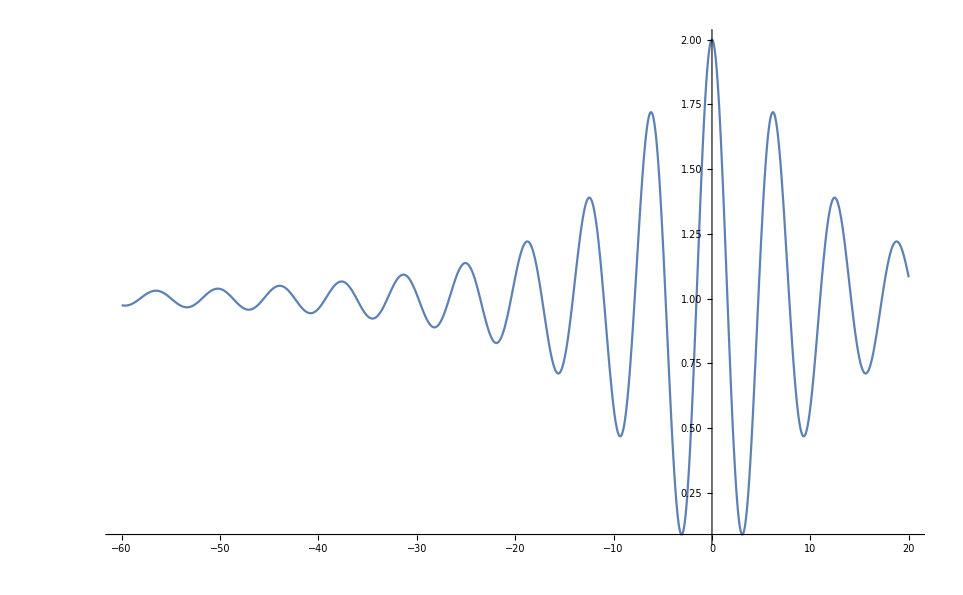

```mathematica
Plot[ffit[x], {x, -60,20}]
```

```mathematica
len = 10
```

10

```mathematica
space = 100
```

100

```mathematica
fpheno = PhenotypeFuncGen[100];
```

```mathematica
pop =BinPopGenerator[10,len]
```

{{1,1,1,1,0,0,1,0,1,1},{0,1,0,0,1,0,1,0,1,0},{0,1,1,0,1,0,0,1,0,0},{1,1,1,0,0,0,1,0,0,1},{0,1,0,0,1,0,1,0,0,0},{0,1,1,0,0,1,0,1,0,1},{1,1,1,0,0,1,1,0,1,0},{0,1,0,1,1,1,1,1,1,0},{0,1,1,1,1,0,0,1,0,1},{0,0,1,1,0,0,0,0,1,0}}

```mathematica
ffit[fpheno[pop]]
```

{1.00737,0.998227,0.844462,1.02774,0.906641,0.978324,0.934011,1.02592,0.980467,1.06458}

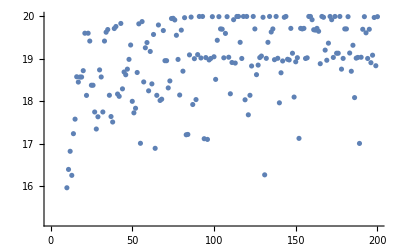

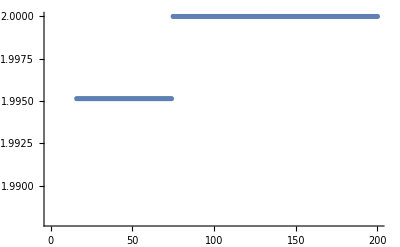

```mathematica
Evolution[200, pop, len, space]
```